```mathematica
neighbourhood[vertex_,graph_]:=Cases[EdgeList[graph],_<->vertex|vertex<->_]/.{x_<->vertex:>x,vertex<->x_:>x}
```

```mathematica
findColoursAtVertex[vertex_,graph_]:=With[{neighbours=neighbourhood[vertex,graph]},
DeleteDuplicates@Flatten[{PropertyValue[{graph,vertex<->#},EdgeStyle],PropertyValue[{graph,#<->vertex},EdgeStyle]}/.$Failed->{}]&/@neighbours//Flatten
]
```

```mathematica
findAdjacentVertexWithColour[vertex_,graph_,colour_]:=With[{neighbours=neighbourhood[vertex,graph]},
Select[neighbours,MemberQ[Flatten@{PropertyValue[{graph,vertex<->#},EdgeStyle]},colour]&][[1]]
]
```

```mathematica
findMissingColour[vertex_,graph_]:=Complement[colours,findColoursAtVertex[vertex,graph]][[1]]
```

```mathematica
fixColours[g_]:=Fold[SetProperty[{#1,#2},VertexStyle->findMissingColour[#2,#1]]&,g,VertexList[g]]
fixColours[]:=Scan[(PropertyValue[{g,#},VertexStyle]=findMissingColour[#,g])&,vertices]
```

```mathematica
transparentComponent[vertex_,graph_]:=First@ConnectedComponents[Graph[VertexList[graph],Select[EdgeList[graph],PropertyValue[{graph,#},EdgeStyle]=!=Transparent&]],{vertex}]
```

```mathematica
edgesBetweenVertices[vertexlist_,g_]:=Select[EdgeList[g],MemberQ[vertexlist,#[[1]]]&&MemberQ[vertexlist,#[[2]]]&]
```

```mathematica
swapColoursOnComponent[vertex_,coloursToSwap_,coloursForComponent_,graph_]:=With[{transp=components[graph,coloursForComponent]},Fold[SetProperty[{#1,#2},EdgeStyle->If[MemberQ[coloursToSwap,First@PropertyValue[{#1,#2},EdgeStyle]],First@PropertyValue[{#1,#2},EdgeStyle]/.{coloursToSwap[[1]]->coloursToSwap[[2]],coloursToSwap[[2]]->coloursToSwap[[1]]},First@PropertyValue[{#1,#2},EdgeStyle]]]&,graph,edgesBetweenVertices[transparentComponent[vertex,transp],transp]]]
```

```mathematica
components[graph_,colours_]:=Fold[SetProperty[{#1,#2},EdgeStyle->If[MemberQ[colours,First@PropertyValue[{#1,#2},EdgeStyle]],First@PropertyValue[{#1,#2},EdgeStyle],Transparent]]&,graph,EdgeList[graph]]
```

```mathematica
vertices=Join[{x,a,b,c,d,e,f},r/@Range[5]];
```

```mathematica
edges={x<->a,x<->b,x<->c,x<->d,x<->e,d<->e,x<->f,r[1]<->a,r[2]<->d,r[3]<->d,r[3]<->r[2],d<->c,b<->r[1],d<->r[4],b<->r[3],a<->r[5]};
```

Take our graph with degree 6.

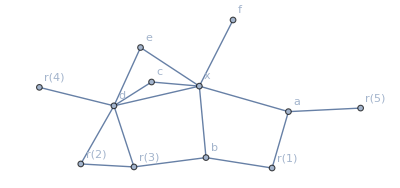

```mathematica
Graph[vertices,edges,VertexLabels->"Name"]
```

```mathematica
colours={Green,Blue,Red,Orange,Purple,Pink,Black};
```

Let’s suppose for induction we have a 7-edge-colouring of the graph if we remove the edge x<->a:

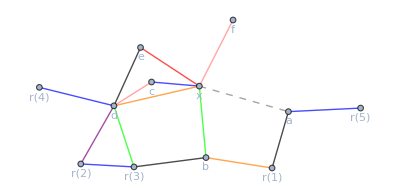

```mathematica
g=Graph[vertices,{Style[x<->a,Dashed],Style[x<->b,Green],Style[x<->c,Blue],Style[x<->d,Orange],Style[x<->e,Red],Style[d<->e,Black],Style[x<->f,Pink],Style[r[1]<->a,Black],Style[r[2]<->d,Purple],Style[r[3]<->d,Green],Style[r[3]<->r[2],Blue],Style[d<->c,Pink],Style[b<->r[1],Orange],Style[d<->r[4],Blue],Style[b<->r[3],Black],Style[a<->r[5],Blue]},VertexLabels->Table[i->Placed[i,Below],{i,vertices}],EdgeStyle->Gray,ImagePadding->10]
```

We want to colour the edge x<->a. (The obvious choice here is to colour it black, but we’ll walk through the algorithm.)

Each vertex has a colour missing from its neighbourhood, because there are at least as many colours as the maximum degree. Display that colour on the node.

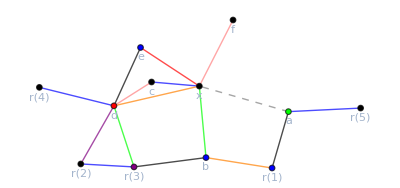

```mathematica
fixColours[];g
```

Let y_1 be the vertex at the end of the missing edge, and let c_1 be its missing colour.

```mathematica
y[1]=a;
```

Let y_2 be a vertex connected to y_1 which has c_1 as the x<->y_2 edge colour:

```mathematica
y[i_]:=findAdjacentVertexWithColour[x,g,c[i-1]]
c[i_]:=findMissingColour[y[i],g]
```

```mathematica
{y[2],c[2]}
```

{b,RGBColor[0, 0, 1]}

Repeat, terminating if ever any c_i=c_j or the colour c_k is missing from x. We wrap this up into a NestWhileList.

```mathematica
NestWhileList[With[{y=findAdjacentVertexWithColour[x,g,#["c"]]},<|"y"->y,"c"->findMissingColour[y,g]|>]&,<|"y"->a,"c"->findMissingColour[a,g]|>,DeleteDuplicates[Last/@Tally[Lookup[{##},"c"]]]==={1}&,All]
```

Part::partw: Part 1 of {} does not exist.

{<|y→a,c→RGBColor[0, 1, 0]|>,<|y→b,c→RGBColor[0, 0, 1]|>,<|y→c,c→GrayLevel[0]|>,<|y→{}⟦1⟧,c→GrayLevel[0]|>}

If the colour c_i is missing from x: we’re done straight away by colouring x<->y_i with colour c_i for all i. Drag the slider below to see the colours appear as we walk along the path:

```mathematica
FoldList[fixColours@SetProperty[{#1,#2["y"]<->x},EdgeStyle->#2["c"]]&,g,Reverse@Most[%]]//ListAnimate
```

Now let’s show an example where this doesn’t fall out so neatly. Let’s take a different colouring, where instead of terminating because c_k is missing from x, we terminate because some c_i=c_j.

```mathematica
gAlt=SetProperty[{g,c<->d},EdgeStyle->Black];
gAlt=SetProperty[{gAlt,d<->e},EdgeStyle->Pink];
gAlt=SetProperty[{gAlt,b<->r[1]},EdgeStyle->Purple];
gAlt=fixColours[gAlt];
```

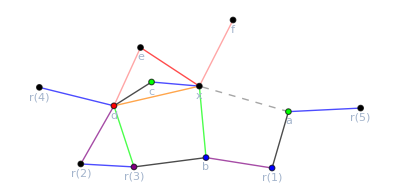

```mathematica
gAlt
```

```mathematica
NestWhileList[With[{y=findAdjacentVertexWithColour[x,gAlt,#["c"]]},<|"y"->y,"c"->findMissingColour[y,gAlt]|>]&,<|"y"->y[1],"c"->findMissingColour[y[1],gAlt]|>,DeleteDuplicates[Last/@Tally[Lookup[{##},"c"]]]==={1}&,All]
```

{<|y→a,c→RGBColor[0, 1, 0]|>,<|y→b,c→RGBColor[0, 0, 1]|>,<|y→c,c→RGBColor[0, 1, 0]|>}

Now we’ve terminated because we’ve hit green again, so we can’t just use the missing colour and chase it back: it’s already in use at the other end of the chain. Considering just the black-green components of the graph, x,y_1,y_3 all have degree 1 (since black or green is missing at all of them), but no vertex in the components can have degree more than 2 (because we’re only allowing black or green edges, so only two possible edges can go into any given vertex). Hence some y_1 or y_3 is disconnected from x in that component. (In this case, both are: recall c=y_3,a=y_1.)

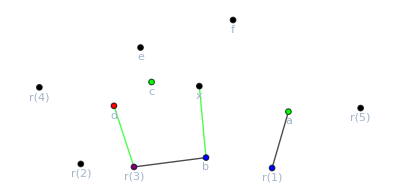

```mathematica
components[gAlt,{Green,Black}]
```

If y_1=a is disconnected from x in the black-green component, we may swap c_1for c_x on the a-component, then colour x<->a in colour c_x.

```mathematica
gAlt
```

-Graphics-

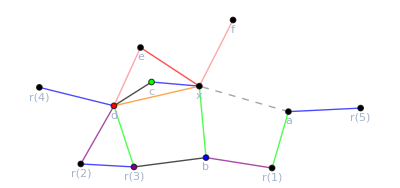

```mathematica
gAlt=swapColoursOnComponent[a,{Green,Black},{Green,Black},gAlt]//fixColours
```

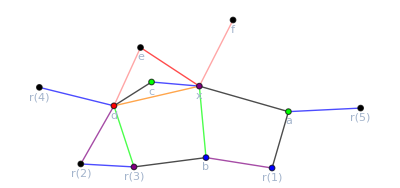

```mathematica
gAlt=SetProperty[{gAlt,x<->a},EdgeStyle->cx];
fixColours[gAlt]
```

And this completes the colouring.